# ICCS Clone

## Parameters

```mathematica
(*Constants*)
mc2=0.511*10^6; (*electron mass eV/c^2*)
me=9.11*10^-31; (*electron mass kg*)
c=299792458; (*SI*)
r0=2.8179403262*10^-15; (*SI*)
echarge=1.60217662*10^-19; (*SI*)
ϵ0=8.8541878128*10^-12; (*SI*)
hbar=6.5821*10^-16; (*in eV s*)
```

```mathematica
(*Source Parameters*)
θa=0.435*10^-3; (*semiangle of collimator - our collimation angle*)
τ=10*10^-12; (*pulse duraction of laser*)
λ=1064*10^-9;
Epulse=62*10^-6;
f=325*10^6;
σL=25*10^-6;
```

## Electron Bunch Momentum Distribution

When a tracked distribution is not available: 
 p_i=pδ(0,1)√ϵ_i/β_i 
can be used to create a distribution where δ(0,1) is a Gaussian distributed random variable with zero mean and unit variance, i=x,y,z.

```mathematica
(*Need to pull the distribution into an array here, where we can easily select px,py,pz*)
```

```mathematica
momdist=Import["C:/Users/user/Documents/Wolfram Mathematica/Bmad_ICCS_data/mom_dat_0.5%.txt","Words"];
```

```mathematica
Npart=Length[momdist]/3;
```

```mathematica
(*Creation of Data Array*)
momdata=Array[m,{3,Npart}];
```

```mathematica
For[i=1,i<(Npart+1),i++,
(*px*)
momdata⟦1,i⟧=Interpreter["Number"][ToString[momdist⟦1+3*(i-1)⟧]];
(*py*)
momdata⟦2,i⟧=Interpreter["Number"][ToString[momdist⟦2+3*(i-1)⟧]];
(*pz*)
momdata⟦3,i⟧=Interpreter["Number"][ToString[momdist⟦3+3*(i-1)⟧]];
];
```

## Intermediaries

cθ is cosθ, sθ is sinθ, cosθ and sinθ are used this way as integral is over cosθ. px, py, pz are the momentum values of a particular particle.

```mathematica
pbar[px_,py_,pz_]:=Sqrt[px^2+py^2+pz^2];
γ[px_,py_,pz_]:=Sqrt[1+(pbar[px,py,pz]/(me*c))^2];
β[px_,py_,pz_]:=pbar[px,py,pz]/(γ[px,py,pz]*me*c);
sθ[cθ_]:=Sqrt[1-cθ^2];
σ[τ_,λ_]:=(τ*c)/λ;
a0[λ_,Epulse_,f_,σL_]:=0.85*10^-9*(λ*10^6)*Sqrt[(Epulse*f)/(2*π*(σL*10^2)^2)];
```

```mathematica
Eevspart=Table[Sqrt[(1/(5.36*10^-28)*pbar[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧])^2+mc2^2],{i,1,Npart}];
```

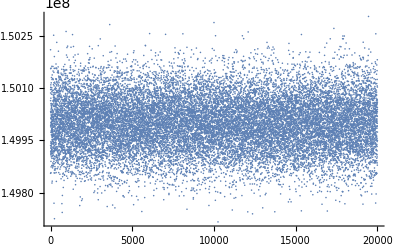

```mathematica
ListPlot[Eevspart]
```

## Scattered Photon Energy

```mathematica
EL[λ_]:=(2*π*hbar*c)/λ;
Xrec[px_,py_,pz_]:=(4*γ[px,py,pz]*EL[λ])/mc2;
```

```mathematica
(*Head-on case only implemented, uses cos^-1 as integral performed for cosθ*)
Eγ[px_,py_,pz_,λ_,cθ_]:=(4*γ[px,py,pz]^2*EL[λ])/(1+γ[px,py,pz]^2*ArcCos[cθ]^2+Xrec[px,py,pz]);
```

```mathematica
Eγ[momdata⟦1,23⟧,momdata⟦2,23⟧,momdata⟦3,23⟧,λ,1]
```

402386.

## Angular Frequency + Frame Change

```mathematica
ω[px_,py_,pz_,λ_,cθ_,ϕ_]:=(Eγ[px,py,pz,λ,cθ]/hbar*(1-β[px,py,pz]/pbar[px,py,pz]*(px*sθ[cθ]*Cos[ϕ]+py*sθ[cθ]*Sin[ϕ]+pz*cθ)))/(1+(β[px,py,pz]*pz)/pbar[px,py,pz]-Eγ[px,py,pz,λ,cθ]/(γ[px,py,pz]*mc2)*(1+cθ));
```

```mathematica
dω[px_,py_,pz_,λ_,cθ_,ϕ_]:=(1+β[px,py,pz]/pbar[px,py,pz]*(px*sθ[cθ]*Cos[ϕ]+py*sθ[cθ]*Sin[ϕ]+pz*cθ)-(β[px,py,pz]^2*pz)/pbar[px,py,pz]^2*(px*sθ[cθ]*Cos[ϕ]+py*sθ[cθ]+pz*cθ))/(1+(β[px,py,pz]*pz)/pbar[px,py,pz]-Eγ[px,py,pz,λ,cθ]/(γ[px,py,pz]*mc2)*(1+cθ));
```

```mathematica
ωvspart=Table[ω[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0],{i,1,Npart}];
```

```mathematica
ELdif=hbar*(Max[ωvspart]-Min[ωvspart])
```

0.0607674

```mathematica
ELmin=hbar*Min[ωvspart]
```

1.14656

```mathematica
ELmax=hbar*Max[ωvspart]
```

1.20733

```mathematica
(*For some reason this is only looking at EL's above my value.*)
```

```mathematica
kc=Table[(2*π*c)/λ,{i,1,Npart}];
```

```mathematica
ListPlot[{ωvspart,kc},PlotRange->Full]
```

-Graphics-

```mathematica
recωvspart=Table[(ω[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0]-(2*π*c)/λ),{i,1,Npart}];
```

```mathematica
Min[recωvspart]
```

-2.84063×10^13

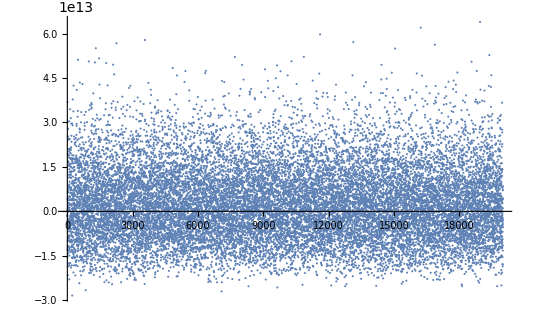

```mathematica
ListPlot[recωvspart]
```

## Electric Field Terms

```mathematica
(*Prefactor*)
prefac[λ_,Epulse_,f_,σL_,τ_]:=(a0[λ,Epulse,f,σL]*c*me*σ[τ,λ]*λ)/echarge^2*Sqrt[π/2];
```

```mathematica
(*ω term*)
ωtermpart=Table[ω[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0],{i,1,Npart}];
```

```mathematica
ListPlot[ωtermpart]
```

-Graphics-

```mathematica
(*prefactor of exp1 term*)
(-(σ[τ,λ]*λ)^2)/(2*c^2);
```

```mathematica
recωvspart2=Table[(ω[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0]-(2*π*c)/λ)^2,{i,1,Npart}];
```

```mathematica
ListPlot[recωvspart2]
```

-Graphics-

```mathematica
(*Exponential Term 1 Logarithm*)
arg1[px_,py_,pz_,λ_,cθ_,ϕ_,τ_]:=(-(σ[τ,λ]*λ)^2)/(2*c^2)*(ω[px,py,pz,λ,cθ,ϕ]-(2*π*c)/λ)^2;
```

```mathematica
arg1partθa=Table[arg1[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0,τ],{i,1,Npart}];
```

```mathematica
arg1part0=Table[arg1[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,1,0,τ],{i,1,Npart}];
```

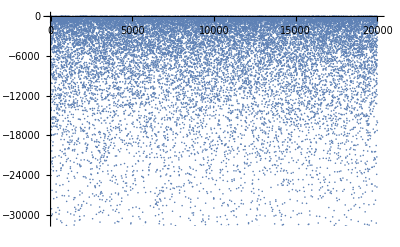

```mathematica
ListPlot[arg1partθa]
```

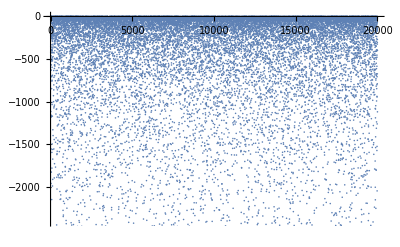

```mathematica
ListPlot[arg1part0]
```

```mathematica
Min[arg1partθa]
```

-204262.

```mathematica
Max[arg1part0]
```

-0.00526733

```mathematica
(*First Exponential term, recωvspart looks at the (ω-kc) term*)
expterm1[px_,py_,pz_,λ_,cθ_,ϕ_,τ_]:=Exp[(-(σ[τ,λ]*λ)^2)/(2*c^2)*(ω[px,py,pz,λ,cθ,ϕ]-(2*π*c)/λ)^2];
```

```mathematica
exp1partθa=Table[expterm1[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0,τ],{i,1,Npart}];
```

```mathematica
Min[exp1partθa]
```

9.83662662×10^-88711

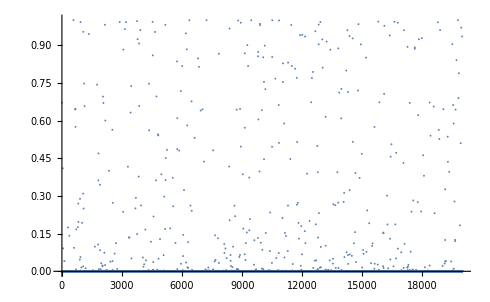

```mathematica
ListPlot[exp1partθa,PlotRange->Full]
```

```mathematica
exp1part0=Table[expterm1[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,1,0,τ],{i,1,Npart}];
```

```mathematica
Max[exp1part0]
```

0.994747

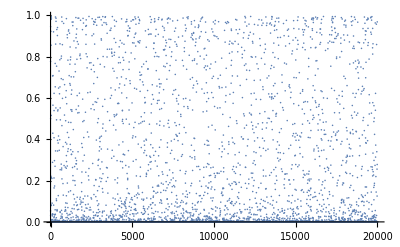

```mathematica
ListPlot[exp1part0,PlotRange->Full]
```

```mathematica
(*Second Exponential Term*)
```

```mathematica
arg2[px_,py_,pz_,λ_,cθ_,ϕ_,τ_]:=(-4*π*σ[τ,λ]^2*λ*ω[px,py,pz,λ,cθ,ϕ])/c;
```

```mathematica
arg2partθa=Table[arg2[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0,τ],{i,1,Npart}];
```

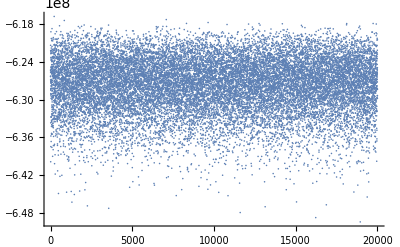

```mathematica
ListPlot[arg2partθa,PlotRange->Full]
```

```mathematica
arg2part0=Table[arg2[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,1,0,τ],{i,1,Npart}];
```

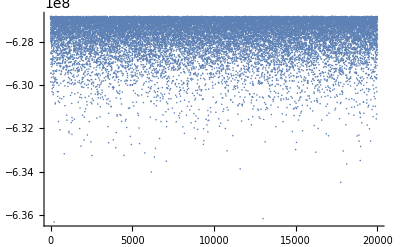

```mathematica
ListPlot[arg2part0,PlotRange->Full]
```

```mathematica
expterm2[px_,py_,pz_,λ_,cθ_,ϕ_,τ_]:=Chop[Exp[(-4*π*σ[τ,λ]^2*λ*ω[px,py,pz,λ,cθ,ϕ])/c]]+1;
```

```mathematica
(*Implemented a chop within this funtion for when σ is small i.e we have
```

```mathematica
exp2partθa=Table[expterm2[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0,τ],{i,1,Npart}];
```

```mathematica
Max[exp2partθa]
```

1

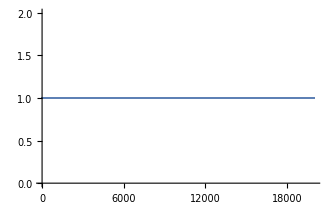

```mathematica
ListPlot[exp2partθa]
```

```mathematica
exp2part0=Table[expterm2[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,1,0,τ],{i,1,Npart}];
```

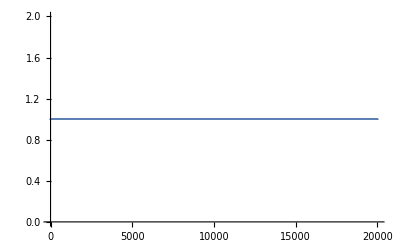

```mathematica
ListPlot[exp2part0]
```

## Electric Field

```mathematica
Elec[px_,py_,pz_,cθ_,ϕ_,Epulse_,f_,σL_,τ_,λ_]:=(a0[λ,Epulse,f,σL]*c*me*σ[τ,λ]*λ)/echarge^2*Sqrt[π/2]*ω[px,py,pz,λ,cθ,ϕ]*Exp[(-(σ[τ,λ]*λ)^2)/(2*c^2)*(ω[px,py,pz,λ,cθ,ϕ]-(2*π*c)/λ)^2]*(Chop[Exp[(-4*π*σ[τ,λ]^2*λ*ω[px,py,pz,λ,cθ,ϕ])/c]]+1);
```

```mathematica
Elecvspart=Table[Elec[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,Cos[θa],0,Epulse,f,σL,τ,λ],{i,1,Npart}];
```

```mathematica
Max[Elecvspart]
```

1.44986×10^24

```mathematica
Min[Elecvspart]
```

1.47766293449943×10^-88686

```mathematica
ListPlot[Elecvspart,PlotRange->Full]
```

-Graphics-

## Interaction Cross Section

```mathematica
(*Term 0*)
X0[px_,py_,pz_,λ_,cθ_,ϕ_]:=((1+cθ-(Eγ[px,py,pz,λ,cθ]/(γ[px,py,pz]*mc2)*(1+cθ)))/(1-β[px,py,px]/pbar[px,py,pz]*(px*sθ[cθ]*Cos[ϕ]+py*sθ[cθ]*Sin[ϕ]+pz*cθ)))^2;
```

```mathematica
X0θa=Table[X0[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0],{i,1,Npart}];
```

```mathematica
X01=Table[X0[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,1⟧,λ,1,0],{i,1,Npart}];
```

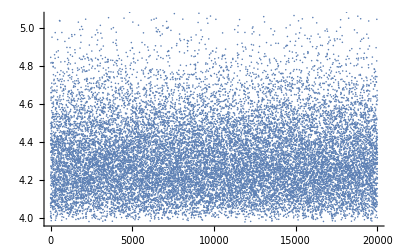

```mathematica
ListPlot[X0θa]
```

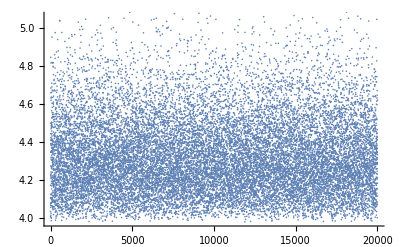

```mathematica
ListPlot[X01]
```

```mathematica
(*Term 1*) 
X1[px_,py_,pz_,λ_,cθ_]:=(1+cθ-((Eγ[px,py,pz,λ,cθ]/(γ[px,py,pz]*mc2))*(1+cθ)))/(1+β[px,py,pz]);
```

```mathematica
X1θa=Table[X1[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa]],{i,1,Npart}];
```

```mathematica
X10=Table[X1[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,1],{i,1,Npart}];
```

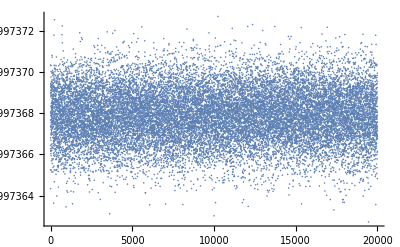

```mathematica
ListPlot[X1θa]
```

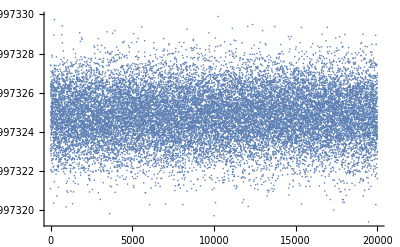

```mathematica
ListPlot[X10]
```

```mathematica
(*Term 2*)
X2[px_,py_,pz_,cθ_,ϕ_]:=(2*(me*sθ[cθ]*Cos[ϕ])^2)/(γ[px,py,pz]*me-1/c*(px*sθ[cθ]*Cos[ϕ]+py*sθ[cθ]*Sin[ϕ]+pz*cθ))^2;
```

```mathematica
X2θa=Table[X2[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,Cos[θa],0],{i,1,Npart}];
```

```mathematica
X20=Table[X2[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,1,0],{i,1,Npart}];
```

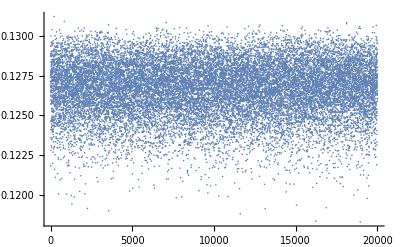

```mathematica
ListPlot[X2θa]
```

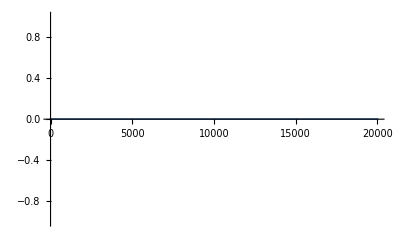

```mathematica
ListPlot[X20]
```

Expected that X20 has zero values as sθ reliance on top.

```mathematica
(*Term 3*)
X3[px_,py_,pz_,cθ_,ϕ_]:=((2*me)^2*c*px*sθ[cθ]*(1+cθ)*Cos[ϕ])/((γ[px,py,pz]*me+pz/c)*(γ[px,py,pz]*me*c-px*sθ[cθ]*Cos[ϕ]-py*sθ[cθ]*Sin[ϕ]-pz*cθ)^2);
```

```mathematica
X3θa=Table[X3[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,Cos[θa],0],{i,1,Npart}];
```

```mathematica
X30=Table[X3[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,1,0],{i,1,Npart}];
```

```mathematica
Max[X3θa]
```

0.251578

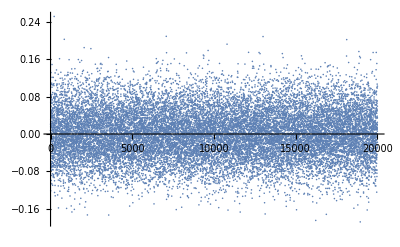

```mathematica
ListPlot[X3θa]
```

```mathematica
ListPlot[X30]
```

-Graphics-

sinθ term in the numerator means that X30 should be zero for this case.

```mathematica
(*Term 4*)
X4[px_,py_,pz_,cθ_,ϕ_]:=(2*(me*px*(1+cθ))^2)/((γ[px,py,pz]*me*c+pz/c)*(γ[px,py,pz]*me*c-px*sθ[cθ]*Cos[ϕ]-py*sθ[cθ]*Sin[ϕ]-pz*cθ))^2;
```

```mathematica
X4θa=Table[X4[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,Cos[θa],0],{i,1,Npart}];
```

```mathematica
X40=Table[X4[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,1,0],{i,1,Npart}];
```

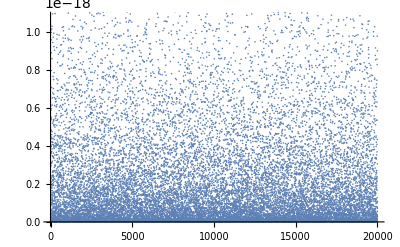

```mathematica
ListPlot[X4θa]
```

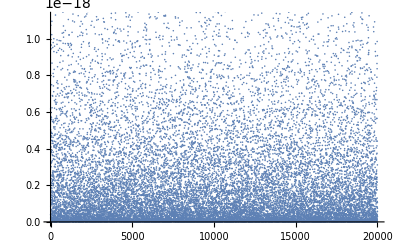

```mathematica
ListPlot[X40]
```

```mathematica
DSXterms[px_,py_,pz_,λ_,cθ_,ϕ_]:=X0[px,py,pz,λ,cθ,ϕ]*(X1[px,py,pz,λ,cθ]+1/X1[px,py,pz,λ,cθ]-X2[px,py,pz,cθ,ϕ]+X3[px,py,pz,cθ,ϕ]-X4[px,py,pz,cθ,ϕ]);
```

```mathematica
Termsθa=Table[DSXterms[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0],{i,1,Npart}];
```

```mathematica
Terms0=Table[DSXterms[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,1,0],{i,1,Npart}];
```

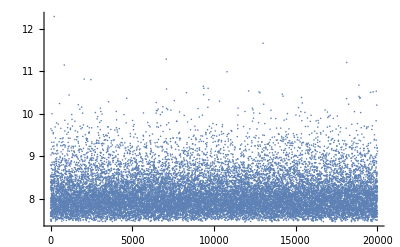

```mathematica
ListPlot[Termsθa,PlotRange->Full]
```

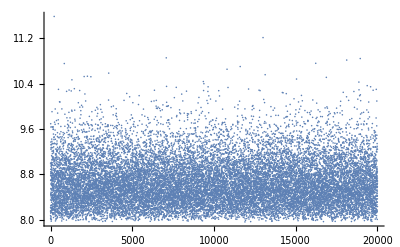

```mathematica
ListPlot[Terms0,PlotRange->Full]
```

```mathematica
dσdΩ[px_,py_,pz_,λ_,cθ_,ϕ_]:=1/2*(r0/(γ[px,py,pz]*(1+β[px,py,pz])))^2*X0[px,py,pz,λ,cθ,ϕ]*(X1[px,py,pz,λ,cθ]+1/X1[px,py,pz,λ,cθ]-X2[px,py,pz,cθ,ϕ]+X3[px,py,pz,cθ,ϕ]-X4[px,py,pz,cθ,ϕ]);
```

```mathematica
dσdΩθa=Table[dσdΩ[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0],{i,1,Npart}];
```

```mathematica
dσdΩ0=Table[dσdΩ[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,1,0],{i,1,Npart}];
```

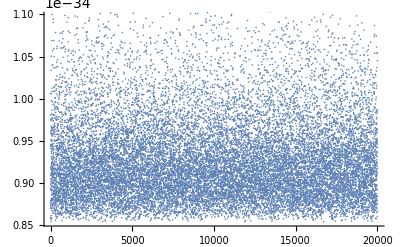

```mathematica
ListPlot[dσdΩθa]
```

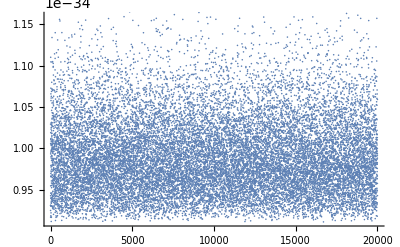

```mathematica
ListPlot[dσdΩ0]
```

## Energy Spectra Single Particle

```mathematica
INTterm[px_,py_,pz_,cθ_,ϕ_,Epulse_,f_,σL_,τ_,λ_]:=Abs[Elec[px,py,pz,cθ,ϕ,Epulse,f,σL,τ,λ]^2]*dσdΩ[px,py,pz,λ,cθ,ϕ]*(Eγ[px,py,pz,λ,cθ]/hbar)/ω[px,py,pz,λ,cθ,ϕ]*dω[px,py,pz,λ,cθ,ϕ];
```

```mathematica
multipart=Table[INTterm[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,Cos[θa],0,Epulse,f,σL,τ,λ],{i,1,Npart}];
```

```mathematica
ListPlot[multipart,PlotRange->Full]
```

-Graphics-

```mathematica
Position[multipart,Max[multipart]]
```

{{10843}}

```mathematica
phipart=Table[{ϕ,INTterm[momdata⟦1,10842⟧,momdata⟦2,10842⟧,momdata⟦3,10842⟧,Cos[θa],ϕ,Epulse,f,σL,τ,λ]},{ϕ,0,0.1,0.001}];
```

```mathematica
phipart
```

{{0.,8.40742×10^18},{0.001,6.52687×10^18},{0.002,4.95723×10^18},{0.003,3.68352×10^18},{0.004,2.67778×10^18},{0.005,1.90446×10^18},{0.006,1.32511×10^18},{0.007,9.0201×10^17},{0.008,6.00691×10^17},{0.009,3.91353×10^17},{0.01,2.49438×10^17},{0.011,1.55535×10^17},{0.012,9.48781×10^16},{0.013,5.66206×10^16},{0.014,3.3056×10^16},{0.015,1.88796×10^16},{0.016,1.05487×10^16},{0.017,5.76596×10^15},{0.018,3.0832×10^15},{0.019,1.61285×10^15},{0.02,8.25362×10^14},{0.021,4.13192×10^14},{0.022,2.02355×10^14},{0.023,9.69463×10^13},{0.024,4.54359×10^13},{0.025,2.08315×10^13},{0.026,9.34308×10^12},{0.027,4.09929×10^12},{0.028,1.75944×10^12},{0.029,7.38734×10^11},{0.03,3.03421×10^11},{0.031,1.21913×10^11},{0.032,4.79175×10^10},{0.033,1.84238×10^10},{0.034,6.9296×10^9},{0.035,2.54963×10^9},{0.036,9.17659×10^8},{0.037,3.23093×10^8},{0.038,1.11278×10^8},{0.039,3.74912×10^7},{0.04,1.23562×10^7},{0.041,3.98358×10^6},{0.042,1.25631×10^6},{0.043,387573.},{0.044,116962.},{0.045,34527.7},{0.046,9970.65},{0.047,2816.5},{0.048,778.269},{0.049,210.367},{0.05,55.623},{0.051,14.3867},{0.052,3.63998},{0.053,0.900876},{0.054,0.218103},{0.055,0.0516519},{0.056,0.0119657},{0.057,0.00271156},{0.058,0.000601075},{0.059,0.000130338},{0.06,0.0000276462},{0.061,5.73626×10^-6},{0.062,1.16427×10^-6},{0.063,2.31156×10^-7},{0.064,4.48937×10^-8},{0.065,8.52892×10^-9},{0.066,1.58502×10^-9},{0.067,2.8814×10^-10},{0.068,5.12389×10^-11},{0.069,8.91307×10^-12},{0.07,1.51666×10^-12},{0.071,2.5245×10^-13},{0.072,4.11052×10^-14},{0.073,6.5471×10^-15},{0.074,1.02008×10^-15},{0.075,1.55472×10^-16},{0.076,2.31794×10^-17},{0.077,3.38054×10^-18},{0.078,4.8229×10^-19},{0.079,6.73071×10^-20},{0.08,9.18871×10^-21},{0.081,1.22711×10^-21},{0.082,1.60306×10^-22},{0.083,2.04859×10^-23},{0.084,2.56093×10^-24},{0.085,3.13172×10^-25},{0.086,3.74639×10^-26},{0.087,4.38413×10^-27},{0.088,5.01873×10^-28},{0.089,5.62024×10^-29},{0.09,6.15689×10^-30},{0.091,6.59802×10^-31},{0.092,6.91689×10^-32},{0.093,7.0935×10^-33},{0.094,7.11645×10^-34},{0.095,6.98412×10^-35},{0.096,6.70534×10^-36},{0.097,6.29766×10^-37},{0.098,5.78627×10^-38},{0.099,5.20083×10^-39},{0.1,4.57311×10^-40}}

```mathematica
ListPlot[phipart,PlotRange->Full]
```

-Graphics-

```mathematica
ninterm=Table[NIntegrate[INTterm[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,Cos[θa],ϕ,Epulse,f,σL,τ,λ],{ϕ,0,2*π}],{i,1,Npart}];
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
dNdωϕ[px_,py_,pz_,cθ_,Epulse_,f_,σL_,τ_,λ_]:=1/Eγ[px,py,pz,λ,cθ]*(ϵ0*c)/(2*π)*NIntegrate[INTterm[px,py,pz,cθ,ϕ,Epulse,f,σL,τ,λ],{ϕ,0,2*π}];
```

```mathematica
SingleParticleSpectrum=Table[dNdωϕ[momdata⟦1,1⟧,momdata⟦2,1⟧,momdata⟦3,1⟧,cθ,Epulse,f,σL,τ,λ],{cθ,Cos[θa],1}];
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
(*For loop over each particle - sum results, table of energies -> which order?? -> energies (cθ) then sum particles*)
```

```mathematica
dNdωp=Table[dNdωϕ[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,cθ,Epulse,f,σL,τ,λ],{cθ,Cos[θa],1},{i,1,Npart}];
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]